# Chaotic Signature in DNA

## Mehdi Ameri - Ferdowsi University of Mashhad

E-mail: amerimehdi9755@gmail.com

## Definitions

```mathematica
pGUE[s_]:=(32/Pi^2)*s^2*Exp[-(4/Pi)*s^2];
cdfGUE[s_]:=GammaRegularized[3/2,0,(4/Pi)*s^2];

pGOE[s_]:=(Pi/2)*s*Exp[-(Pi/4)*s^2];
cdfGOE[s_]:=1-Exp[-(Pi/4)*s^2];

pGSE[s_]:=(2^18/(3^6*Pi^3))*s^4*Exp[-(64/(9*Pi))*s^2];
cdfGSE[s_]:=GammaRegularized[5/2,0,(64/(9*Pi))*s^2];

pPoisson[s_]:=Exp[-s];
cdfPoisson[s_]:=1-Exp[-s];

pSP[s_]:=4*s*Exp[-2*s];
```

```mathematica
(* DEFINE UNFOLDING& NORMALIZATION FUNCTION FOR A SINGLE FILE *)
ProcessSingleFile[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,nTotal,trimCount,coreLevels,nCore,kdeDist,unfoldedLevels,spacings,meanS,normSpacings},importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];

(* Extract energy column *)
rawEnergies=ToExpression[Rest[importedData][[All,5]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
nTotal=Length[sortedLevels];
If[nTotal<20,Return[{}]];

(* Band-edge trimming (outer 10%)*)
trimCount=Floor[0.1*nTotal];
coreLevels=Take[sortedLevels,{trimCount+1,nTotal-trimCount}];
nCore=Length[coreLevels];
If[nCore<10,Return[{}]];

(* Gaussian KDE Unfolding *)
kdeDist=SmoothKernelDistribution[coreLevels];
unfoldedLevels=Table[nCore*CDF[kdeDist,e],{e,coreLevels}];

(* Spacings& Local Normalization *)
spacings=Differences[unfoldedLevels];
If[Length[spacings]==0,Return[{}]];
meanS=Mean[spacings];
If[meanS≤0||!NumberQ[meanS],Return[{}]];
normSpacings=spacings/meanS;

(* Filter strictly within plot range boundary *)
Select[normSpacings,(#>0)&]]
```

```mathematica
(* DEFINE FUNCTION TO COMPUTE r-VALUES FOR A SINGLE FILE*)

ProcessSingleFileForR[filePath_]:=Module[{importedData,rawEnergies,sortedLevels,rawSpacings,rValues},(*Import CSV as raw Data table*)importedData=Import[filePath,"Data"];
If[Length[importedData]≤1,Return[{}]];
(*Extract column 4 ("orbital_energy_hartree") and clean*)rawEnergies=ToExpression[Rest[importedData][[All,4]]];
sortedLevels=Sort[N[DeleteCases[rawEnergies,_Missing|Null|""|_String]]];
If[Length[sortedLevels]<10,Return[{}]];(*Skip files with too few levels*)(*Compute consecutive raw spacings s_i=E_{i+1}-E_i*)rawSpacings=Differences[sortedLevels];
If[Length[rawSpacings]<2,Return[{}]];
(*Compute adjacent-gap ratios r_i=Min(s_i,s_{i+1})/Max(s_i,s_{i+1})*)rValues=Table[Min[rawSpacings[[i]],rawSpacings[[i+1]]]/Max[rawSpacings[[i]],rawSpacings[[i+1]]],{i,1,Length[rawSpacings]-1}];
rValues];
```

```mathematica
(*  NUMBER VARIANCE: INTERVAL COUNTING *)

(* Count levels in intervals[x,x+L)*)

intervalCounts[levels_List,starts_List,len_?NumericQ]:=Module[{n=Length[levels],left=1,right=1,counts=ConstantArray[0,Length[starts]],t},Do[t=starts[[j]];
While[left≤n&&levels[[left]]<t,left++];
If[right<left,right=left];
While[right≤n&&levels[[right]]<t+len,right++];
counts[[j]]=right-left;,{j,Length[starts]}];
counts];


(*Number variance for one geometry*)

numberVarianceOne[levels_List,L_?NumericQ,nStarts_Integer,edgeTrim_?NumericQ]:=Module[{u,tMin,tMax,starts,counts},u=Sort[N[levels]];
If[Length[u]<2||L≤0,Return[Missing["Invalid"]]];
(*Remove edge regions*)tMin=First[u]+edgeTrim;
tMax=Last[u]-L-edgeTrim;
If[tMax≤tMin,Return[Missing["TooShort"]]];
(*Generate equally spaced window positions*)starts=N[Subdivide[tMin,tMax,nStarts]];
(*Count levels in all windows*)counts=intervalCounts[u,starts,L];
(*Calculate number variance*)Mean[(counts-L)^2]];

(* ENSEMBLE AVERAGING *)

numberVarianceEnsemble[unfolded_List,Lvals_List,nStarts_Integer,edgeTrim_?NumericQ]:=Table[Module[{vals},vals=Select[numberVarianceOne[#,ell,nStarts,edgeTrim]&/@unfolded,NumericQ];
If[Length[vals]≥2,{ell,Mean[vals],StandardDeviation[vals]/Sqrt[Length[vals]],Length[vals]},{ell,Indeterminate,Indeterminate,Length[vals]}]],{ell,Lvals}];
```

```mathematica
sigmaPoisson[L_]:=L;
sigmaSemiPoisson[L_]:=L/2+(1-Exp[-4*L])/8;sigmaGOE[L_]:=(2/Pi^2)*(Log[2*Pi*L]+EulerGamma+1-Pi^2/8);

(* sigmaPoisson[L_?NumericQ]:=L;
sigmaSemiPoisson[L_?NumericQ]:=L/2+(1-Exp[-4 L])/8;
sigmaGUE[L_?NumericQ]:=(Log[2 Pi L]+EulerGamma+1-Cos[2 Pi L]-CosIntegral[2 Pi L])/Pi^2+L (1-2 SinIntegral[2 Pi L]/Pi);
sigmaGOE[L_?NumericQ]:=2 sigmaGUE[L]+SinIntegral[Pi L]^2/Pi^2-SinIntegral[Pi L]/Pi; *)
```

```mathematica
ATHBfilePaths=FileNames["Your AT-HB Directory\\frame_*.csv"];
Print["Total files found: ",Length[ATHBfilePaths]];
```

```mathematica
GCHBfilePaths=FileNames["Your GC-HB Directory\\frame_*.csv"];
Print["Total files found: ",Length[GCHBfilePaths]];
```

```mathematica
BothHBfilePaths=Join[ATHBfilePaths,GCHBfilePaths];
%//Length
```

```mathematica
ATMMfilePaths=FileNames["Your AT-MM Directory\\multimode_sample_*.csv"];
Print["Total files found: ",Length[ATMMfilePaths]];
```

```mathematica
GCMMfilePaths=FileNames["Your GC-MM Directory\\multimode_sample_*.csv"];
Print["Total files found: ",Length[GCMMfilePaths]];
```

```mathematica
BothMMfilePaths=Join[ATMMfilePaths,GCMMfilePaths];
%//Length
```

## Probability Distribution

### H-Bond

#### AT

```mathematica
(*EXTRACT ALL ORBITAL ENERGIES*)

allEnergies=Flatten[Table[data=Import[file,"CSV"];
Select[Rest[data][[All,5]],NumericQ],{file,ATHBfilePaths}]];

(* MINIMUM AND MAXIMUM Values *)

Print["Total orbital energies: ",Length[allEnergies]];
Print["Minimum orbital energy (eV): ",Min[allEnergies]];
Print["Maximum orbital energy (eV): ",Max[allEnergies]];
```

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDE=Flatten[ParallelTable[ProcessSingleFile[file],{file,ATHBfilePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDE]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDE]]];
```

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDE]]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDE]]
```

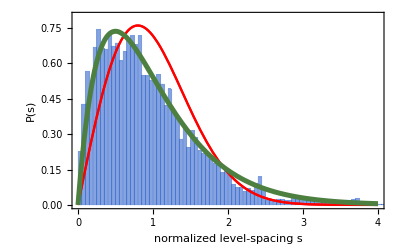

```mathematica
(* Generate Customized Plot *)
ATHBOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

#### GC

```mathematica
(*EXTRACT ALL ORBITAL ENERGIES*)

allEnergies=Flatten[Table[data=Import[file,"CSV"];
Select[Rest[data][[All,5]],NumericQ],{file,GCHBfilePaths}]];

(*CALCULATE MINIMUM AND MAXIMUM*)

Print["Total orbital energies: ",Length[allEnergies]];
Print["Minimum orbital energy (eV): ",Min[allEnergies]];
Print["Maximum orbital energy (eV): ",Max[allEnergies]];
```

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDE=Flatten[ParallelTable[ProcessSingleFile[file],{file,GCHBfilePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDE]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDE]]];
```

Total pooled normalized spacings across all files: 253000

Ensemble Mean Spacing: 1.

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDE]]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDE]]
```

Maximum value of spacings: 9.94629 ev

Minimum value of spacings: 0.00152653 ev

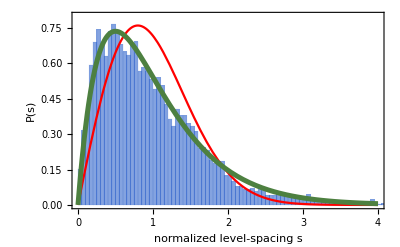

```mathematica
(* Generate Customized Plot *)
GCHBOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

#### Both

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDEBoth=Flatten[ParallelTable[ProcessSingleFile[file],{file,BothHBfilePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDEBoth]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDEBoth]]];
```

Total pooled normalized spacings across all files: 502191

Ensemble Mean Spacing: 0.931292

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDEBoth]]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDEBoth]]
```

Maximum value of spacings: 3.49968 ev

Minimum value of spacings: 0.000487664 ev

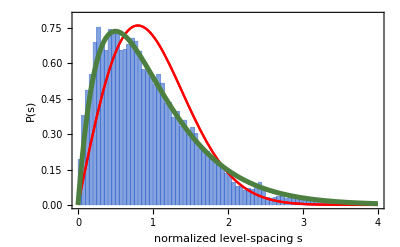

```mathematica
(* Generate Customized Plot *)
BothHBOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDEBoth,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

#### Export

```mathematica
Export["Your Directory\\ATHBOrbEnergyKDEUnfNoTitle.png",ATHBOrbEnergyKDEUnfNoTitle,ImageResolution->300];
Export["Your Directory\\GCHBOrbEnergyKDEUnfNoTitle.png",GCHBOrbEnergyKDEUnfNoTitle,ImageResolution->300];
Export["Your Directory\\BothHBOrbEnergyKDEUnfNoTitle.png",BothHBOrbEnergyKDEUnfNoTitle,ImageResolution->300];
```

### Multimode

#### AT

```mathematica
(*EXTRACT ALL ORBITAL ENERGIES*)

allEnergies=Flatten[Table[data=Import[file,"CSV"];
Select[Rest[data][[All,5]],NumericQ],{file,ATMMfilePaths}]];

(*CALCULATE MINIMUM AND MAXIMUM*)

Print["Total orbital energies: ",Length[allEnergies]];
Print["Minimum orbital energy (eV): ",Min[allEnergies]];
Print["Maximum orbital energy (eV): ",Max[allEnergies]];
```

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDE=Flatten[ParallelTable[ProcessSingleFile[file],{file,ATMMfilePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDE]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDE]]];
```

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDE]]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDE]]
```

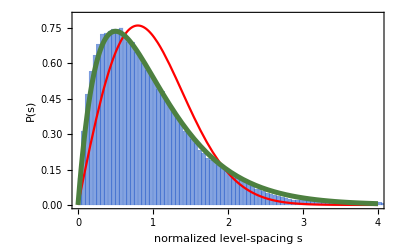

```mathematica
(* Generate Customized Plot *)
ATMMOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,(*Dashed,*)Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

#### GC

```mathematica
(*EXTRACT ALL ORBITAL ENERGIES*)

allEnergies=Flatten[Table[data=Import[file,"CSV"];
Select[Rest[data][[All,5]],NumericQ],{file,GCMMfilePaths}]];


(*CALCULATE MINIMUM AND MAXIMUM*)

Print["Total orbital energies: ",Length[allEnergies]];
Print["Minimum orbital energy (eV): ",Min[allEnergies]];
Print["Maximum orbital energy (eV): ",Max[allEnergies]];
```

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDE=Flatten[ParallelTable[ProcessSingleFile[file],{file,GCMMfilePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDE]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDE]]];
```

Total pooled normalized spacings across all files: 253000

Ensemble Mean Spacing: 1.

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDE]]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDE]]
```

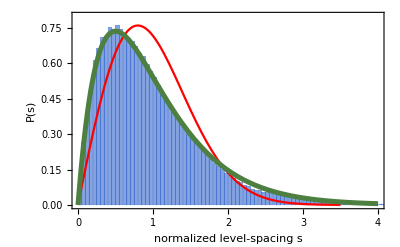

```mathematica
(* Generate Customized Plot *)
GCMMOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDE,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},
Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,3.5},PlotStyle->Directive[Red,(*Dashed,*)Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

#### Both

```mathematica
(* PROCESS ALL FILES IN PARALLEL AND FLATTEN *)
AllSpacingsKDEBoth=Flatten[ParallelTable[ProcessSingleFile[file],{file,BothMMfilePaths}]];

Print["Total pooled normalized spacings across all files: ",Length[AllSpacingsKDEBoth]];
Print["Ensemble Mean Spacing: ",N[Mean[AllSpacingsKDEBoth]]];
```

Total pooled normalized spacings across all files: 503175

Ensemble Mean Spacing: 0.939949

```mathematica
Print[ "Maximum value of spacings: ",Max[AllSpacingsKDEBoth]]
Print[ "Minimum value of spacings: ",Min[AllSpacingsKDEBoth]]
```

Maximum value of spacings: 3.49995 ev

Minimum value of spacings: 0.00101639 ev

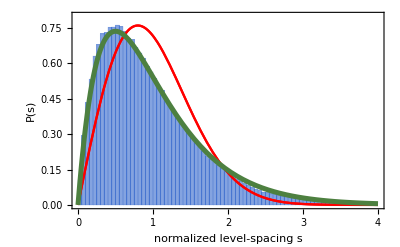

```mathematica
(* Generate Customized Plot *)
BothMMOrbEnergyKDEUnfNoTitle=Histogram[AllSpacingsKDEBoth,{0.05},"PDF",
ChartStyle->Directive[RGBColor[0.2,0.4,0.8],Opacity[0.6]],PlotRange->{{0,4},{0,0.8}},Frame->True,
FrameStyle->Directive[RGBColor[0.1,0.1,0.1],Thickness[0.005]],
BaseStyle->{FontSize->9,FontFamily->"Arial",FontWeight->Bold,Black},
FrameLabel->{Style["normalized level-spacing s",10,Bold,FontFamily->"Arial",Black],
Style["P(s)",10,Bold,FontFamily->"Arial",Black]},Epilog->{{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Red,,Thickness[0.005],Plot[pGOE[x],{x,0,4},PlotStyle->Directive[Red,Thick]][[1]]},{Green,Thickness[0.005],Plot[pSP[x],{x,0,4},PlotStyle->Directive[RGBColor[0.3,0.5,0.25],Thickness[0.009]]][[1]]}}]
```

#### Export

```mathematica
Export["Your Directory\\ATMMOrbEnergyKDEUnfNoTitle.png",ATMMOrbEnergyKDEUnfNoTitle,ImageResolution->300];
Export["Your Directory\\GCMMOrbEnergyKDEUnfNoTitle.png",GCMMOrbEnergyKDEUnfNoTitle,ImageResolution->300];
Export["Your Directory\\BothMMOrbEnergyKDEUnfNoTitle.png",BothMMOrbEnergyKDEUnfNoTitle,ImageResolution->300];
```

## Adjacent-gap ratios

### AT-HB

```mathematica
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,ATHBfilePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for AT-HB <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@ATHBfilePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

```mathematica
Print[StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]*100 ," %"]
```

### GC-HB

```mathematica
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,GCHBfilePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for GC-HB <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@GCHBfilePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

### Both-HB

```mathematica
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,BothHBfilePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for Both-HB <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@BothHBfilePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

### AT-MM

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,ATMMfilePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for AT-MM <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@ATMMfilePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

### GC-MM

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,GCMMfilePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for GC-MM <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@GCMMfilePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

### Both-MM

```mathematica
(*3. PROCESS ALL FILES IN PARALLEL AND FLATTEN*)
allRValues=Flatten[ParallelTable[ProcessSingleFileForR[file],{file,BothMMfilePaths}]];

Print["Total pooled r-values across all files: ",Length[allRValues]];
If[Length[allRValues]>0,Print["Ensemble Mean Adjacent-Gap Ratio for both-MM <r>: ",N[Mean[allRValues]]],Print["Warning: allRValues is empty. Please check file paths and format."]];
```

```mathematica
fileMeans=DeleteCases[ProcessSingleFileForR/@BothMMfilePaths,_?(_=={})];
fileMeans=Mean/@fileMeans;

Print["Mean of file-level <r>: ",Mean[fileMeans]];
Print["Standard Error of the Mean: ",StandardDeviation[fileMeans]/Sqrt[Length[fileMeans]]];
```

## Number Variance

#### AT-HB

```mathematica
(* CSV file pattern *)
filePattern="frame_*.csv";
orbitalSelection="All";
kdeBandwidth="Silverman";
Lvalues=Range[0.5,20,0.5];
nStarts=150;
edgeTrim=5;
minLevels=50;
```

```mathematica
folder=SystemDialogInput["Directory"];
If[folder===$Canceled,Abort[]];
files=Sort@FileNames[filePattern,folder];
Print["Files found: ",Length[files]];
If[files==={},Print["No CSV files found. Check the folder and file pattern."];
Abort[];];
If[!MemberQ[{"All","Occupied","Virtual"},orbitalSelection],Print["Invalid orbital selection."];
Abort[];];
```

Files found: 1000

```mathematica
readSpectrum[file_]:=Module[{data,rows,selectedRows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
(*Remove header and select valid rows*)rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&&(orbitalSelection==="All"||NumericQ[#[[2]]])&];
(*Select occupied,virtual,or all orbitals*)selectedRows=Switch[orbitalSelection,"All",rows,"Occupied",Select[rows,#[[2]]>0&],"Virtual",Select[rows,#[[2]]==0&]];
If[selectedRows==={},Return[$Failed]];
(*Extract orbital energies in eV:column 5*)energies=N[selectedRows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
If[!VectorQ[energies,TrueQ[Im[#]==0]&],Return[$Failed]];
Sort[Re[energies]]];
```

```mathematica
(*IMPORT ALL SPECTRA*)

rawSpectra=readSpectrum/@files;
validMask=ListQ/@rawSpectra;
spectra=Pick[rawSpectra,validMask];
validFiles=Pick[files,validMask];
Print["Valid spectra: ",Length[spectra]];
Print["Invalid files: ",Length[files]-Length[spectra]];
If[spectra==={},Print["No valid spectra found."];
Abort[];];

(*CHECK ORBITAL COUNTS*)

spectrumLengths=Length/@spectra;
Print["Orbital counts: ",Tally[spectrumLengths]];
If[Length[DeleteDuplicates[spectrumLengths]]≠1,Print["Error: Different numbers of orbitals per geometry."];
Abort[];];
nLevels=First[spectrumLengths];
If[nLevels<minLevels,Print["Insufficient number of orbitals."];
Abort[];];
Print["Orbitals per geometry: ",nLevels];
```

```mathematica
(*Combine all orbital energies*)

allEnergies=Flatten[spectra];
Print["Total pooled energies: ",Length[allEnergies]];

(*Construct ONE KDE from the entire ensemble*)

commonKDE=Quiet@Check[SmoothKernelDistribution[allEnergies,kdeBandwidth],$Failed];
If[commonKDE===$Failed,Print["KDE construction failed."];
Abort[];];

(*Calculate the common cumulative density*)

commonCDFValues=N[CDF[commonKDE,#]&/@allEnergies];
If[!VectorQ[commonCDFValues,NumericQ],Print["Error in evaluating the common KDE CDF."];
Abort[];];
```

```mathematica
(*  UNFOLD EACH GEOMETRY USING THE SAME KDE*)

(* Multiply the common CDF by the number of orbitals per geometry,NOT the total number of pooled energies *)

unfoldedFlat=nLevels commonCDFValues;

(* Restore the original geometry boundaries *)

unfoldedSpectra=Partition[unfoldedFlat,nLevels];

(* Sort individual unfolded spectra *)

unfoldedSpectra=Sort/@unfoldedSpectra;

Print["Common ensemble KDE unfolding completed."];
Print["Number of unfolded spectra: ",Length[unfoldedSpectra]];
```

```mathematica
(* CALCULATE NUMBER VARIANCE FOR THE ENSEMBLE *)

Print["Calculating number variance..."];

commonKDEResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];


(*Extract results*)

commonKDEMean=commonKDEResults[[All,2]];
commonKDESE=commonKDEResults[[All,3]];
nContributing=commonKDEResults[[All,4]];


Print["Number variance calculation completed."];
Print["Minimum contributing geometries: ",Min[nContributing]];
Print["Maximum contributing geometries: ",Max[nContributing]];
```

```mathematica
(* THEORETICAL NUMBER VARIANCE CURVES *)

(* Generate theoretical curves *)

poissonCurve=Table[{L,sigmaPoisson[L]},{L,Lvalues}];
semiPoissonCurve=Table[{L,sigmaSemiPoisson[L]},{L,Lvalues}];
GOECurve=Table[{L,sigmaGOE[L]},{L,Lvalues}];

(* Empirical KDE curve *)
empiricalCurve=Select[commonKDEResults[[All,{1,2}]],NumericQ[#[[2]]]&];
```

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];


(* NUMBER VARIANCE PLOT *)

ATHBNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["Your Directory\\ATHBNV.png",ATHBNV,ImageResolution->300];
```

```mathematica
GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];
PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];
SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];


(*RESULTS TABLE*)
Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

```mathematica
(* SPECTRAL COMPRESSIBILITY *)

(* SELECT LARGE-L FITTING RANGE *)
fitLmin=5;
fitLmax=20;

(* FUNCTION TO CALCULATE LINEAR SLOPE *)

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];


(* CALCULATE SPECTRAL COMPRESSIBILITY *)

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];


(* DISPLAY RESULTS *)

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"AT HB",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

#### GC-HB

```mathematica
(*CSV file pattern*)
filePattern="frame_*.csv";
orbitalSelection="All";
kdeBandwidth="Silverman";
Lvalues=Range[0.5,20,0.5];
nStarts=150;
edgeTrim=5;
minLevels=50;
```

```mathematica
folder=SystemDialogInput["Directory"];
If[folder===$Canceled,Abort[]];
files=Sort@FileNames[filePattern,folder];
Print["Files found: ",Length[files]];
If[files==={},Print["No CSV files found. Check the folder and file pattern."];
Abort[];];
If[!MemberQ[{"All","Occupied","Virtual"},orbitalSelection],Print["Invalid orbital selection."];
Abort[];];
```

Files found: 1000

```mathematica
readSpectrum[file_]:=Module[{data,rows,selectedRows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
(*Remove header and select valid rows*)rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&&(orbitalSelection==="All"||NumericQ[#[[2]]])&];
(*Select occupied,virtual,or all orbitals*)selectedRows=Switch[orbitalSelection,"All",rows,"Occupied",Select[rows,#[[2]]>0&],"Virtual",Select[rows,#[[2]]==0&]];
If[selectedRows==={},Return[$Failed]];
(*Extract orbital energies in eV:column 5*)energies=N[selectedRows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
If[!VectorQ[energies,TrueQ[Im[#]==0]&],Return[$Failed]];
Sort[Re[energies]]];
```

```mathematica
(* IMPORT ALL SPECTRA *)

rawSpectra=readSpectrum/@files;
validMask=ListQ/@rawSpectra;
spectra=Pick[rawSpectra,validMask];
validFiles=Pick[files,validMask];
Print["Valid spectra: ",Length[spectra]];
Print["Invalid files: ",Length[files]-Length[spectra]];
If[spectra==={},Print["No valid spectra found."];
Abort[];];


(* CHECK ORBITAL COUNTS *)

spectrumLengths=Length/@spectra;
Print["Orbital counts: ",Tally[spectrumLengths]];
If[Length[DeleteDuplicates[spectrumLengths]]≠1,Print["Error: Different numbers of orbitals per geometry."];
Abort[];];
nLevels=First[spectrumLengths];
If[nLevels<minLevels,Print["Insufficient number of orbitals."];
Abort[];];
Print["Orbitals per geometry: ",nLevels];
```

Valid spectra: 1000

Invalid files: 0

Orbital counts: {{316,1000}}

Orbitals per geometry: 316

```mathematica
(*  CONSTRUCT THE COMMON ENSEMBLE KDE *)

(*Combine all orbital energies*)

allEnergies=Flatten[spectra];
Print["Total pooled energies: ",Length[allEnergies]];

(*Construct ONE KDE from the entire ensemble*)

commonKDE=Quiet@Check[SmoothKernelDistribution[allEnergies,kdeBandwidth],$Failed];
If[commonKDE===$Failed,Print["KDE construction failed."];
Abort[];];

(*Calculate the common cumulative density*)

commonCDFValues=N[CDF[commonKDE,#]&/@allEnergies];
If[!VectorQ[commonCDFValues,NumericQ],Print["Error in evaluating the common KDE CDF."];
Abort[];];
```

Total pooled energies: 316000

```mathematica
(*  UNFOLD EACH GEOMETRY USING THE SAME KDE*)

(* Multiply the common CDF by the number of orbitals per geometry,NOT the total number of pooled energies *)

unfoldedFlat=nLevels commonCDFValues;

(*Restore the original geometry boundaries*)

unfoldedSpectra=Partition[unfoldedFlat,nLevels];

(*Sort individual unfolded spectra*)

unfoldedSpectra=Sort/@unfoldedSpectra;

Print["Common ensemble KDE unfolding completed."];
Print["Number of unfolded spectra: ",Length[unfoldedSpectra]];
```

Common ensemble KDE unfolding completed.

Number of unfolded spectra: 1000

```mathematica
(* CALCULATE NUMBER VARIANCE FOR THE ENSEMBLE *) 

Print["Calculating number variance..."];

commonKDEResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];


(*Extract results*)

commonKDEMean=commonKDEResults[[All,2]];
commonKDESE=commonKDEResults[[All,3]];
nContributing=commonKDEResults[[All,4]];


Print["Number variance calculation completed."];
Print["Minimum contributing geometries: ",Min[nContributing]];
Print["Maximum contributing geometries: ",Max[nContributing]];
```

```mathematica
(* THEORETICAL NUMBER VARIANCE CURVES *)

(*Generate theoretical curves*)

poissonCurve=Table[{L,sigmaPoisson[L]},{L,Lvalues}];
semiPoissonCurve=Table[{L,sigmaSemiPoisson[L]},{L,Lvalues}];
GOECurve=Table[{L,sigmaGOE[L]},{L,Lvalues}];

(*Empirical KDE curve*)

empiricalCurve=Select[commonKDEResults[[All,{1,2}]],NumericQ[#[[2]]]&];
```

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];

(* NUMBER VARIANCE PLOT *) 

GCHBNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["Your Directory\\GCHBNV.png",GCHBNV,ImageResolution->300];
```

```mathematica
GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];
PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];
SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];


(*RESULTS TABLE*)
Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

```mathematica
(*SPECTRAL COMPRESSIBILITY*)

fitLmin=5;
fitLmax=20;

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"GC HB",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

#### Both-HB

```mathematica
(*AT DIRECTORY*)
atFolder="AT-HB Directory";

(*GC DIRECTORY*)
gcFolder="GC-HB Directory";

(*CSV FILE PATTERN*)
filePattern="frame_*.csv";

(*FIND FILES IN EACH DIRECTORY INDEPENDENTLY*)

atFiles=Sort@FileNames[filePattern,atFolder];
gcFiles=Sort@FileNames[filePattern,gcFolder];

(*COMBINE THE TWO FILE LISTS*)

files=Join[atFiles,gcFiles];

Print["AT files: ",Length[atFiles]];
Print["GC files: ",Length[gcFiles]];
Print["Total files: ",Length[files]];

If[files==={},Abort[]];
```

```mathematica
(*EXTRACT ALL ORBITAL ENERGIES*)readSpectrum[file_]:=Module[{data,rows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&];
If[rows==={},Return[$Failed]];
energies=N[rows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
Sort[energies]];


(*IMPORT AT AND GC SEPARATELY*)

atRawSpectra=readSpectrum/@atFiles;
gcRawSpectra=readSpectrum/@gcFiles;


(* KEEP ONLY SUCCESSFULLY IMPORTED SPECTRA *)

atSpectra=Select[atRawSpectra,ListQ];
gcSpectra=Select[gcRawSpectra,ListQ];


(*COMBINE THE INDIVIDUAL SPECTRA*)

spectra=Join[atSpectra,gcSpectra];

Print["Valid AT spectra: ",Length[atSpectra]];
Print["Valid GC spectra: ",Length[gcSpectra]];
Print["Total valid spectra: ",Length[spectra]];
Print["Orbital counts: ",Tally[Length/@spectra]];

If[spectra==={},Abort[]];
```

```mathematica
(*POOL ALL AT AND GC ENERGIES*)
allEnergies=Flatten[spectra];

(*AVERAGE NUMBER OF ORBITALS PER GEOMETRY*)

meanLevels=Mean[Length/@spectra];


(*COMMON ENSEMBLE KDE*)

kdeBandwidth="Silverman";
commonKDE=SmoothKernelDistribution[allEnergies,kdeBandwidth];

(*APPLY THE SAME UNFOLDING FUNCTION TO EVERY SPECTRUM*)

unfoldingFunction[E_?NumericQ]:=meanLevels CDF[commonKDE,E];

(*PRESERVE INDIVIDUAL GEOMETRY BOUNDARIES*)

unfoldedSpectra=(unfoldingFunction/@#)&/@spectra;

Print["Combined AT + GC unfolding completed."];
Print["Total geometries: ",Length[unfoldedSpectra]];
```

```mathematica
Lvalues=Range[0.5,20,0.5];
nStarts=150;
edgeTrim=5;
```

```mathematica
(* COMBINED AT+GC NUMBER VARIANCE *) 

Lvalues=N[Range[0.5,20,0.5]];
nStarts=150;
edgeTrim=5;


Print["Calculating combined AT + GC number variance..."];

combinedResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];

(*EXTRACT RESULTS*)

combinedMean=combinedResults[[All,2]];
combinedSE=combinedResults[[All,3]];
nContributing=combinedResults[[All,4]];

(*EMPIRICAL CURVE*)

empiricalCurve=Select[combinedResults[[All,{1,2}]],NumericQ[#[[2]]]&];

Print["Calculation completed."];
Print["Total geometries: ",Length[unfoldedSpectra]];
Print["Minimum contributing geometries: ",Min[nContributing]];
Print["Maximum contributing geometries: ",Max[nContributing]];
```

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];

(* NUMBER VARIANCE PLOT *)

ATGCHBNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["Your Directory\\ATGCHBNV.png",ATGCHBNV,ImageResolution->300];
```

```mathematica
(* MEAN ABSOLUTE ERROR*)

GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];
PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];
SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];


(*RESULTS TABLE*)

Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

Ensemble | Mean Absolute Error
GOE | 2.4425
Poisson | 6.9471
Semi-Poisson | 2.0133

```mathematica
(*SPECTRAL COMPRESSIBILITY*)

fitLmin=5;
fitLmax=20;

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"Both HB",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

#### AT-MM

```mathematica
(*CSV file pattern*)
filePattern="multimode_sample_*.csv";
orbitalSelection="All";
kdeBandwidth="Silverman";
Lvalues=Range[0.5,20,0.5];
nStarts=150;
edgeTrim=5;
minLevels=50;
```

```mathematica
folder=SystemDialogInput["Directory"];
If[folder===$Canceled,Abort[]];
files=Sort@FileNames[filePattern,folder];
Print["Files found: ",Length[files]];
If[files==={},Print["No CSV files found. Check the folder and file pattern."];
Abort[];];
If[!MemberQ[{"All","Occupied","Virtual"},orbitalSelection],Print["Invalid orbital selection."];
Abort[];];
```

Files found: 1000

```mathematica
readSpectrum[file_]:=Module[{data,rows,selectedRows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
(*Remove header and select valid rows*)rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&&(orbitalSelection==="All"||NumericQ[#[[2]]])&];
(*Select occupied,virtual,or all orbitals*)selectedRows=Switch[orbitalSelection,"All",rows,"Occupied",Select[rows,#[[2]]>0&],"Virtual",Select[rows,#[[2]]==0&]];
If[selectedRows==={},Return[$Failed]];
(*Extract orbital energies in eV:column 5*)energies=N[selectedRows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
If[!VectorQ[energies,TrueQ[Im[#]==0]&],Return[$Failed]];
Sort[Re[energies]]];
```

```mathematica
(* IMPORT ALL SPECTRA *)

rawSpectra=readSpectrum/@files;
validMask=ListQ/@rawSpectra;
spectra=Pick[rawSpectra,validMask];
validFiles=Pick[files,validMask];
Print["Valid spectra: ",Length[spectra]];
Print["Invalid files: ",Length[files]-Length[spectra]];
If[spectra==={},Print["No valid spectra found."];
Abort[];];


(*CHECK ORBITAL COUNTS*)

spectrumLengths=Length/@spectra;
Print["Orbital counts: ",Tally[spectrumLengths]];
If[Length[DeleteDuplicates[spectrumLengths]]≠1,Print["Error: Different numbers of orbitals per geometry."];
Abort[];];
nLevels=First[spectrumLengths];
If[nLevels<minLevels,Print["Insufficient number of orbitals."];
Abort[];];
Print["Orbitals per geometry: ",nLevels];
```

```mathematica
(* CONSTRUCT THE COMMON ENSEMBLE KDE*)

(*Combine all orbital energies*)

allEnergies=Flatten[spectra];
Print["Total pooled energies: ",Length[allEnergies]];

(*Construct ONE KDE from the entire ensemble*)

commonKDE=Quiet@Check[SmoothKernelDistribution[allEnergies,kdeBandwidth],$Failed];
If[commonKDE===$Failed,Print["KDE construction failed."];
Abort[];];

(*Calculate the common cumulative density*)

commonCDFValues=N[CDF[commonKDE,#]&/@allEnergies];
If[!VectorQ[commonCDFValues,NumericQ],Print["Error in evaluating the common KDE CDF."];
Abort[];];
```

```mathematica
(* UNFOLD EACH GEOMETRY USING THE SAME KDE*)

(* Multiply the common CDF by the number of orbitals per geometry,NOT the total number of pooled energies *)

unfoldedFlat=nLevels commonCDFValues;

(*Restore the original geometry boundaries*)

unfoldedSpectra=Partition[unfoldedFlat,nLevels];

(*Sort individual unfolded spectra*)

unfoldedSpectra=Sort/@unfoldedSpectra;

Print["Common ensemble KDE unfolding completed."];
Print["Number of unfolded spectra: ",Length[unfoldedSpectra]];
```

```mathematica
(* CALCULATE NUMBER VARIANCE FOR THE ENSEMBLE*)

Print["Calculating number variance..."];

commonKDEResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];

(*Extract results*)

commonKDEMean=commonKDEResults[[All,2]];
commonKDESE=commonKDEResults[[All,3]];
nContributing=commonKDEResults[[All,4]];


Print["Number variance calculation completed."];
Print["Minimum contributing geometries: ",Min[nContributing]];
Print["Maximum contributing geometries: ",Max[nContributing]];
```

```mathematica
(* THEORETICAL NUMBER VARIANCE CURVES*)

(*Generate theoretical curves*)

poissonCurve=Table[{L,sigmaPoisson[L]},{L,Lvalues}];
semiPoissonCurve=Table[{L,sigmaSemiPoisson[L]},{L,Lvalues}];
GOECurve=Table[{L,sigmaGOE[L]},{L,Lvalues}];

(*Empirical KDE curve*)

empiricalCurve=Select[commonKDEResults[[All,{1,2}]],NumericQ[#[[2]]]&];
```

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];


(* ==============================================*)
(*NUMBER VARIANCE PLOT*)
(* ==============================================*)

ATMMNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["Your Directory\\ATMMNV.png",ATMMNV,ImageResolution->300];
```

```mathematica
GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];
PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];
SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];


(*RESULTS TABLE*)
Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

```mathematica
(*SPECTRAL COMPRESSIBILITY*)

fitLmin=5;
fitLmax=20;

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"AT MM",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

#### GC-MM

```mathematica
(*CSV file pattern*)
filePattern="multimode_sample_*.csv";
orbitalSelection="All";
kdeBandwidth="Silverman";
Lvalues=Range[0.5,20,0.5];
nStarts=150;
edgeTrim=5;
minLevels=50;
```

```mathematica
folder=SystemDialogInput["Directory"];
If[folder===$Canceled,Abort[]];
files=Sort@FileNames[filePattern,folder];
Print["Files found: ",Length[files]];
If[files==={},Print["No CSV files found. Check the folder and file pattern."];
Abort[];];
If[!MemberQ[{"All","Occupied","Virtual"},orbitalSelection],Print["Invalid orbital selection."];
Abort[];];
```

Files found: 1000

```mathematica
readSpectrum[file_]:=Module[{data,rows,selectedRows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
(*Remove header and select valid rows*)rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&&(orbitalSelection==="All"||NumericQ[#[[2]]])&];
(*Select occupied,virtual,or all orbitals*)selectedRows=Switch[orbitalSelection,"All",rows,"Occupied",Select[rows,#[[2]]>0&],"Virtual",Select[rows,#[[2]]==0&]];
If[selectedRows==={},Return[$Failed]];
(*Extract orbital energies in eV:column 5*)energies=N[selectedRows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
If[!VectorQ[energies,TrueQ[Im[#]==0]&],Return[$Failed]];
Sort[Re[energies]]];
```

```mathematica
(*IMPORT ALL SPECTRA*)

rawSpectra=readSpectrum/@files;
validMask=ListQ/@rawSpectra;
spectra=Pick[rawSpectra,validMask];
validFiles=Pick[files,validMask];
Print["Valid spectra: ",Length[spectra]];
Print["Invalid files: ",Length[files]-Length[spectra]];
If[spectra==={},Print["No valid spectra found."];
Abort[];];

(*CHECK ORBITAL COUNTS*)

spectrumLengths=Length/@spectra;
Print["Orbital counts: ",Tally[spectrumLengths]];
If[Length[DeleteDuplicates[spectrumLengths]]≠1,Print["Error: Different numbers of orbitals per geometry."];
Abort[];];
nLevels=First[spectrumLengths];
If[nLevels<minLevels,Print["Insufficient number of orbitals."];
Abort[];];
Print["Orbitals per geometry: ",nLevels];
```

```mathematica
(* CONSTRUCT THE COMMON ENSEMBLE KDE*)

(*Combine all orbital energies*)

allEnergies=Flatten[spectra];
Print["Total pooled energies: ",Length[allEnergies]];

(*Construct ONE KDE from the entire ensemble*)

commonKDE=Quiet@Check[SmoothKernelDistribution[allEnergies,kdeBandwidth],$Failed];
If[commonKDE===$Failed,Print["KDE construction failed."];
Abort[];];

(*Calculate the common cumulative density*)

commonCDFValues=N[CDF[commonKDE,#]&/@allEnergies];
If[!VectorQ[commonCDFValues,NumericQ],Print["Error in evaluating the common KDE CDF."];
Abort[];];
```

Total pooled energies: 316000

```mathematica
(* UNFOLD EACH GEOMETRY USING THE SAME KDE*)

(* Multiply the common CDF by the number of orbitals per geometry,NOT the total number of pooled energies *)

unfoldedFlat=nLevels commonCDFValues;

(*Restore the original geometry boundaries*)

unfoldedSpectra=Partition[unfoldedFlat,nLevels];

(*Sort individual unfolded spectra*)

unfoldedSpectra=Sort/@unfoldedSpectra;

Print["Common ensemble KDE unfolding completed."];
Print["Number of unfolded spectra: ",Length[unfoldedSpectra]];
```

```mathematica
(* CALCULATE NUMBER VARIANCE FOR THE ENSEMBLE*)

Print["Calculating number variance..."];

commonKDEResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];

(*Extract results*)

commonKDEMean=commonKDEResults[[All,2]];
commonKDESE=commonKDEResults[[All,3]];
nContributing=commonKDEResults[[All,4]];


Print["Number variance calculation completed."];
Print["Minimum contributing geometries: ",Min[nContributing]];
Print["Maximum contributing geometries: ",Max[nContributing]];
```

```mathematica
(* THEORETICAL NUMBER VARIANCE CURVES *)

(*Generate theoretical curves*)

poissonCurve=Table[{L,sigmaPoisson[L]},{L,Lvalues}];
semiPoissonCurve=Table[{L,sigmaSemiPoisson[L]},{L,Lvalues}];
GOECurve=Table[{L,sigmaGOE[L]},{L,Lvalues}];

(*Empirical KDE curve*)

empiricalCurve=Select[commonKDEResults[[All,{1,2}]],NumericQ[#[[2]]]&];
```

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];

(* NUMBER VARIANCE PLOT *)

GCMMNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["Your Directory\\GCMMNV.png",GCMMNV,ImageResolution->300];
```

```mathematica
GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];
PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];
SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];


(*RESULTS TABLE*)
Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

```mathematica
(*SPECTRAL COMPRESSIBILITY*)

fitLmin=5;
fitLmax=20;

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"GC MM",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

#### Both-MM

```mathematica
(*AT DIRECTORY*)
atFolder="AT-MM Directory";

(*GC DIRECTORY*)
gcFolder="GC-MM Directory";

(*CSV FILE PATTERN*)
filePattern="multimode_sample_*.csv";

(*FIND FILES IN EACH DIRECTORY INDEPENDENTLY*)

atFiles=Sort@FileNames[filePattern,atFolder];
gcFiles=Sort@FileNames[filePattern,gcFolder];

(*COMBINE THE TWO FILE LISTS*)

files=Join[atFiles,gcFiles];

Print["AT files: ",Length[atFiles]];
Print["GC files: ",Length[gcFiles]];
Print["Total files: ",Length[files]];

If[files==={},Abort[]];
```

```mathematica
(*EXTRACT ALL ORBITAL ENERGIES*)readSpectrum[file_]:=Module[{data,rows,energies},data=Quiet@Check[Import[file,"CSV"],$Failed];
If[data===$Failed||!ListQ[data]||Length[data]<2,Return[$Failed]];
rows=Select[Rest[data],ListQ[#]&&Length[#]≥5&&NumericQ[#[[5]]]&];
If[rows==={},Return[$Failed]];
energies=N[rows[[All,5]]];
If[!VectorQ[energies,NumericQ],Return[$Failed]];
Sort[energies]];

(*IMPORT AT AND GC SEPARATELY*)

atRawSpectra=readSpectrum/@atFiles;
gcRawSpectra=readSpectrum/@gcFiles;


(*KEEP ONLY SUCCESSFULLY IMPORTED SPECTRA*)

atSpectra=Select[atRawSpectra,ListQ];
gcSpectra=Select[gcRawSpectra,ListQ];


(*COMBINE THE INDIVIDUAL SPECTRA*)

spectra=Join[atSpectra,gcSpectra];

Print["Valid AT spectra: ",Length[atSpectra]];
Print["Valid GC spectra: ",Length[gcSpectra]];
Print["Total valid spectra: ",Length[spectra]];
Print["Orbital counts: ",Tally[Length/@spectra]];

If[spectra==={},Abort[]];
```

```mathematica
(*POOL ALL AT AND GC ENERGIES*)
allEnergies=Flatten[spectra];

(*AVERAGE NUMBER OF ORBITALS PER GEOMETRY*)

meanLevels=Mean[Length/@spectra];

(*COMMON ENSEMBLE KDE*)

kdeBandwidth="Silverman";
commonKDE=SmoothKernelDistribution[allEnergies,kdeBandwidth];

(*APPLY THE SAME UNFOLDING FUNCTION TO EVERY SPECTRUM*)

unfoldingFunction[E_?NumericQ]:=meanLevels CDF[commonKDE,E];

(*PRESERVE INDIVIDUAL GEOMETRY BOUNDARIES*)

unfoldedSpectra=(unfoldingFunction/@#)&/@spectra;

Print["Combined AT + GC unfolding completed."];
Print["Total geometries: ",Length[unfoldedSpectra]];
```

```mathematica
Lvalues=Range[0.5,20,0.5];
nStarts=150;
edgeTrim=5;
```

```mathematica
(* COMBINED AT+GC NUMBER VARIANCE *)
Lvalues=N[Range[0.5,20,0.5]];
nStarts=150;
edgeTrim=5;

Print["Calculating combined AT + GC number variance..."];

combinedResults=numberVarianceEnsemble[unfoldedSpectra,Lvalues,nStarts,edgeTrim];

(*EXTRACT RESULTS*)

combinedMean=combinedResults[[All,2]];
combinedSE=combinedResults[[All,3]];
nContributing=combinedResults[[All,4]];

(*EMPIRICAL CURVE*)

empiricalCurve=Select[combinedResults[[All,{1,2}]],NumericQ[#[[2]]]&];

Print["Calculation completed."];
Print["Total geometries: ",Length[unfoldedSpectra]];
Print["Minimum contributing geometries: ",Min[nContributing]];
Print["Maximum contributing geometries: ",Max[nContributing]];
```

```mathematica
fontFamily="Times New Roman";
titlesSize=14;
fontSize=12;
lineThickness=2;
imageSize=350;
dataColor=RGBColor[0.85,0.12,0.12];
goeColor=RGBColor[0.1,0.3,0.8];
poissonColor=RGBColor[0.1,0.55,0.25];
semiColor=RGBColor[0.6,0.2,0.65];


(*NUMBER VARIANCE PLOT*)

ATGCMMNV=ListLinePlot[{empiricalCurve,GOECurve,poissonCurve,semiPoissonCurve},PlotStyle->{Directive[dataColor,AbsoluteThickness[lineThickness]],
Directive[goeColor,AbsoluteThickness[lineThickness]],
Directive[poissonColor,Dashed,AbsoluteThickness[lineThickness]],Directive[semiColor,Dashed,AbsoluteThickness[lineThickness]]},Frame->True,Axes->False,FrameLabel->{Style["L",titlesSize,Black,FontFamily->fontFamily],Style["Σ^2(L)",titlesSize,Black,FontFamily->fontFamily]},FrameStyle->Directive[Black,AbsoluteThickness[1.5]],FrameTicksStyle->Directive[Black,AbsoluteThickness[1.5],FontFamily->fontFamily(*,FontSize->fontSize*)],PlotRange->All,ImageSize->imageSize]
```

```mathematica
Export["Your Directory\\ATGCMMNV.png",ATGCMMNV,ImageResolution->300];
```

```mathematica
(* MEAN ABSOLUTE ERROR*) 

GOEDeviation=Mean[Abs[empiricalCurve[[All,2]]-GOECurve[[All,2]]]];

PoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-poissonCurve[[All,2]]]];

SemiPoissonDeviation=Mean[Abs[empiricalCurve[[All,2]]-semiPoissonCurve[[All,2]]]];

(*RESULTS TABLE*)

Grid[{{"Ensemble","Mean Absolute Error"},{"GOE",NumberForm[GOEDeviation,{8,4}]},{"Poisson",NumberForm[PoissonDeviation,{8,4}]},{"Semi-Poisson",NumberForm[SemiPoissonDeviation,{8,4}]}},Frame->All,Alignment->Center]
```

```mathematica
(*SPECTRAL COMPRESSIBILITY*)

fitLmin=5;
fitLmax=20;

spectralCompressibility[curve_]:=Module[{points,fit},points=Select[curve,fitLmin≤#[[1]]≤fitLmax&];
fit=Fit[points,{1,x},x];
Coefficient[fit,x]];

chiData=spectralCompressibility[empiricalCurve];
chiGOE=spectralCompressibility[GOECurve];
chiPoisson=spectralCompressibility[poissonCurve];
chiSemiPoisson=spectralCompressibility[semiPoissonCurve];

Grid[{{"Ensemble","Spectral compressibility (χ)"},{"Both MM",NumberForm[chiData,{6,4}]},{"GOE",NumberForm[chiGOE,{6,4}]},{"Poisson",NumberForm[chiPoisson,{6,4}]},{"Semi-Poisson",NumberForm[chiSemiPoisson,{6,4}]}},Frame->All,Alignment->Center]
```

## Tracy-Widom

```mathematica
(* SELECT THE DATASET: AT OR GC *)

filePaths=FileNames["multimode_sample_*.csv","Copy your directory address here"];

Print["Total files found: ",Length[filePaths]];

(*EXTRACT THE ORIGINAL ORBITAL ENERGIES*)

spectra=Table[Module[{data,energies},data=Import[file,"CSV"];
energies=Cases[Rest[data][[All,5]],_?NumericQ];
If[Length[energies]>0,energies,$Failed]],{file,filePaths}];

(*REMOVE INVALID FILES*)

validSpectra=Select[spectra,ListQ];

Print["Valid spectra: ",Length[validSpectra]];

(*EXTRACT EXTREME EIGENVALUES*)

maxEigenvalues=Max/@validSpectra;
minEigenvalues=Min/@validSpectra;

Print["Number of maximum eigenvalues: ",Length[maxEigenvalues]];
Print["Number of minimum eigenvalues: ",Length[minEigenvalues]];

(*BASIC STATISTICS*)

Print["Maximum eigenvalue range (eV): ",MinMax[maxEigenvalues]];
Print["Minimum eigenvalue range (eV): ",MinMax[minEigenvalues]];
```

```mathematica
(* SELECT TRACY-WIDOM DISTRIBUTION *)

beta=1;
twDist=TracyWidomDistribution[beta];

(*THEORETICAL MEAN AND STANDARD DEVIATION*)

twMean=N[Mean[twDist]];
twSD=N[Sqrt[Variance[twDist]]];
Print["TW mean: ",twMean];
Print["TW standard deviation: ",twSD];
```

```mathematica
zMax=N[(maxEigenvalues-Mean[maxEigenvalues])/StandardDeviation[maxEigenvalues]];
reflectedMin=-minEigenvalues;
zMin=N[(reflectedMin-Mean[reflectedMin])/StandardDeviation[reflectedMin]];
twStandardizedPDF[x_]:=twSD PDF[twDist,twMean+twSD x];
twStandardizedCDF[x_]:=CDF[twDist,twMean+twSD x];
```

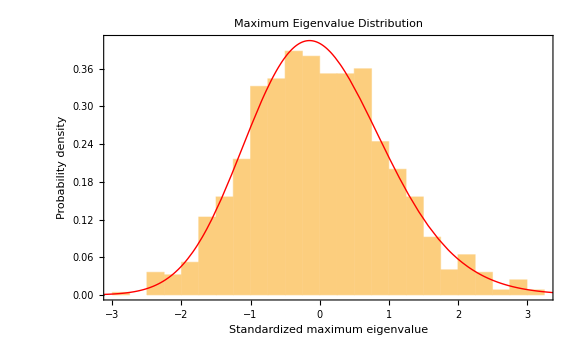

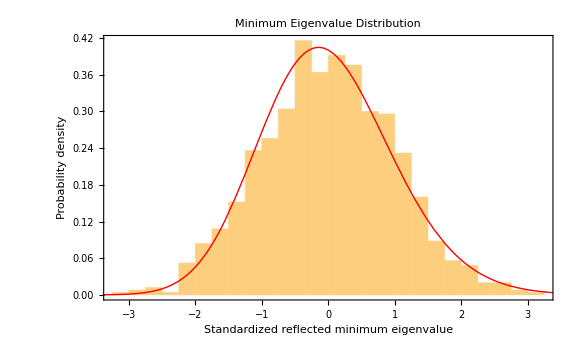

```mathematica
(* Maximum EIGENVALUES *)

maxPlot=Show[Histogram[zMax,{0.25},"PDF"],Plot[twStandardizedPDF[x],{x,Min[zMax]-0.5,Max[zMax]+0.5},PlotStyle->{Red,Thick}],PlotLabel->"Maximum Eigenvalue Distribution",Frame->True,FrameLabel->{"Standardized maximum eigenvalue","Probability density"},PlotLegends->{"Numerical data","Tracy-Widom"},ImageSize->Large];

(* MINIMUM EIGENVALUES *)

minPlot=Show[Histogram[zMin,{0.25},"PDF"],Plot[twStandardizedPDF[x],{x,Min[zMin]-0.5,Max[zMin]+0.5},PlotStyle->{Red,Thick}],PlotLabel->"Minimum Eigenvalue Distribution",Frame->True,FrameLabel->{"Standardized reflected minimum eigenvalue","Probability density"},PlotLegends->{"Numerical data","Tracy-Widom"},ImageSize->Large];

maxPlot
minPlot
```

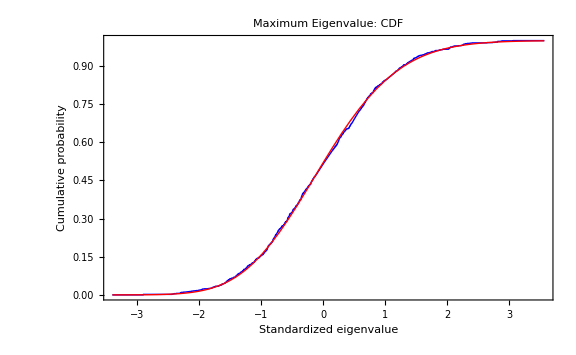

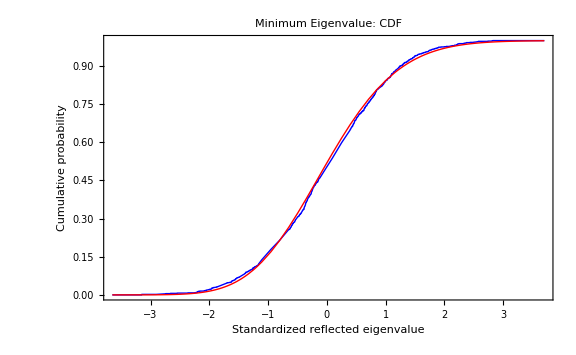

```mathematica
(* CUMULATIVE DISTRIBUTION COMPARISON *)

empiricalCDF[data_List]:=Module[{sorted,n},sorted=Sort[data];
n=Length[sorted];
Interpolation[Join[{{First[sorted]-10^-8,0}},Transpose[{sorted,Range[n]/n}]],InterpolationOrder->0]];

(*MAXIMUM EIGENVALUES*)

maxEmpCDF=empiricalCDF[zMax];

maxCDFPlot=Show[Plot[maxEmpCDF[x],{x,Min[zMax]-0.5,Max[zMax]+0.5},PlotStyle->{Blue,Thick}],Plot[twStandardizedCDF[x],{x,Min[zMax]-0.5,Max[zMax]+0.5},PlotStyle->{Red,Thick}],PlotLabel->"Maximum Eigenvalue: CDF",Frame->True,FrameLabel->{"Standardized eigenvalue","Cumulative probability"},PlotLegends->{"Numerical data","Tracy-Widom"},ImageSize->Large];

(*MINIMUM EIGENVALUES*)

minEmpCDF=empiricalCDF[zMin];

minCDFPlot=Show[Plot[minEmpCDF[x],{x,Min[zMin]-0.5,Max[zMin]+0.5},PlotStyle->{Blue,Thick}],Plot[twStandardizedCDF[x],{x,Min[zMin]-0.5,Max[zMin]+0.5},PlotStyle->{Red,Thick}],PlotLabel->"Minimum Eigenvalue: CDF",Frame->True,FrameLabel->{"Standardized reflected eigenvalue","Cumulative probability"},PlotLegends->{"Numerical data","Tracy-Widom"},ImageSize->Large];

maxCDFPlot
minCDFPlot
```

```mathematica
KSdistance[data_List,theoreticalCDF_]:=Module[{sorted,n,i,dPlus,dMinus},sorted=Sort[data];
n=Length[sorted];
dPlus=Max[Table[i/n-theoreticalCDF[sorted[[i]]],{i,n}]];
dMinus=Max[Table[theoreticalCDF[sorted[[i]]]-(i-1)/n,{i,n}]];
Max[dPlus,dMinus]];

maxKS=KSdistance[zMax,twStandardizedCDF];

minKS=KSdistance[zMin,twStandardizedCDF];

Print["Maximum eigenvalue KS distance: ",maxKS];

Print["Minimum eigenvalue KS distance: ",minKS];
```

Maximum eigenvalue KS distance: 0.0230868

Minimum eigenvalue KS distance: 0.0271438

```mathematica
Print["Number of geometries: ",Length[validSpectra]];

Print["Orbital counts per geometry: ",DeleteDuplicates[Length/@validSpectra]];

Print["Maximum eigenvalue statistics:"];
Print["Mean = ",N[Mean[maxEigenvalues]]];
Print["SD = ",N[StandardDeviation[maxEigenvalues]]];

Print["Minimum eigenvalue statistics:"];
Print["Mean = ",N[Mean[minEigenvalues]]];
Print["SD = ",N[StandardDeviation[minEigenvalues]]];

Print["TW beta = ",beta];
Print["TW mean = ",twMean];
Print["TW SD = ",twSD];
```

```mathematica
(* SKEWNESS AND KURTOSIS COMPARISON*)

Print["TRACY-WIDOM THEORETICAL VALUES"];

Print["TW1 skewness = ",N[Skewness[twDist]]];
Print["TW1 kurtosis = ",N[Kurtosis[twDist]]];

Print[""];

Print["MAXIMUM EIGENVALUE DISTRIBUTION"];

Print["Skewness = ",N[Skewness[zMax]]];

Print["Kurtosis = ",N[Kurtosis[zMax]]];

Print[""];

Print["MINIMUM EIGENVALUE DISTRIBUTION"];
Print["Skewness = ",N[Skewness[zMin]]];
Print["Kurtosis = ",N[Kurtosis[zMin]]];
```